```mathematica
Needs["Parallel`Queue`Priority`"]
```

```mathematica
Unprotect@Priority; Clear[Priority];
Priority[p_] := -p[[2]];
HCEIPS[N_, lambda_, p_, rho0_, T_] :=
Block[{eta, queue, x, y, ed, t, ptot, gen, accp},
ed = ExponentialDistribution[1/lambda];
eta = rho0;
queue = priorityQueue[];
Do[
If [eta[[x]] == 1,
t = RandomVariate[ed];
If[t ≤ T, EnQueue[queue, {x, t}], Null], Null],
{x, 1, N}
];
While[Not[EmptyQ[queue]],
{x, t} = DeQueue[queue];
ptot = Sum[(1-eta[[y]] )* p[x, y], {y, 1, N}];
gen = RandomReal[] * ptot;
accp = 0;
Do[If[eta[[y]] == 0,
	accp = accp + p[x,y];
	If[accp > gen,
		eta[[x]] = 0; eta[[y]]  = 1; x = y; Break[],
		Null]
,Null], {y, 1, N}];
t = t + RandomVariate[ed];
If[t ≤ T, EnQueue[queue, {x,t}], Null]
];
eta]
```

```mathematica
StartState[N_, nu_] := RandomSample[Join[ConstantArray[1, nu], ConstantArray[0, N-nu]]];
TSim[N_, lambda_, T_, nu_, attempts_]:=
	Sum[
	Module[{ss = StartState[N, nu]},
	Timing[HCEIPS[N, lambda, Function[{x,y},1], ss, T]][[1]]],
		{i, 1, attempts}]/attempts
```

```mathematica
TSim[100, 1, 100, 50, 5]
```

2.25

```mathematica
Table[{T, TSim[100, 1, T, 50, 5]}, {T, {1, 5, 10, 30, 50, 75, 100}}]
```

{{1,0.01875},{5,0.103125},{10,0.196875},{30,0.59375},{50,1.00938},{75,1.49375},{100,2.11875}}

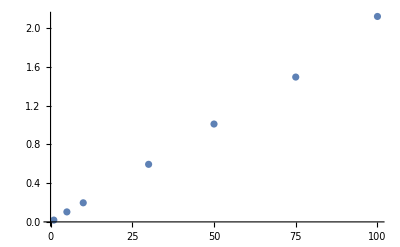

```mathematica
ListPlot[Out[8]]
```

```mathematica
Table[{N, TSim[N, 1, 100, 25, 5]}, {N, {25, 75, 100, 200, 300}}]
```

{{25,0.440625},{75,0.740625},{100,0.921875},{200,1.525},{300,2.47813}}

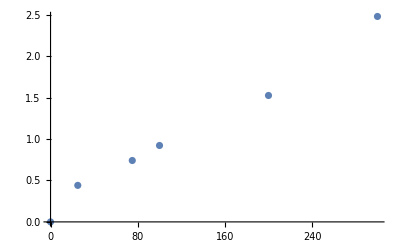

```mathematica
ListPlot[Append[%28, {0,0}]]
```

```mathematica
Table[{nu, TSim[100, 1, 100, nu, 5]}, {nu, {1, 5, 10,25, 50, 75, 100}}]
```

{{1,0.034375},{5,0.16875},{10,0.3625},{25,0.91875},{50,1.79688},{75,2.83125},{100,4.19375}}

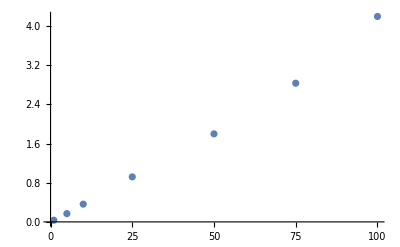

```mathematica
ListPlot[%23]
```

```mathematica
TSim[400, 1, 100, 25, 5]
```

3.05

```mathematica
TSim[500, 1, 100, 25, 5]
```

3.7125

```mathematica
TSim[600, 1, 100, 25, 5]
```

5.30313

```mathematica
NumberForm[5.3031250000000005,16]
```

5.303125

```mathematica
HCELIPS[N_, lambda_, p_, rho0_, T_] :=
Block[{eta, queue, x, y, ed, t, ptot, gen, accp, neighbours},
ed = ExponentialDistribution[1/lambda];
eta = rho0;
queue = priorityQueue[];
Do[
If [eta[[x]] == 1,
t = RandomVariate[ed];
If[t ≤ T, EnQueue[queue, {x, t}], Null], Null],
{x, 1, N}
];
While[Not[EmptyQ[queue]],
{x, t} = DeQueue[queue];
neighbours = {Mod[x-1, N, 1], Mod[x+1, N, 1]};
ptot = Sum[(1-eta[[y]] )* p[x, y], {y,neighbours}];
gen = RandomReal[] * ptot;
accp = 0;
Do[If[eta[[y]] == 0,
	accp = accp + p[x,y];
	If[accp > gen,
		eta[[x]] = 0; eta[[y]]  = 1; x = y; Break[],
		Null]
,Null], {y, neighbours}];
t = t + RandomVariate[ed];
If[t ≤ T, EnQueue[queue, {x,t}], Null]
];
eta]
```

```mathematica
TSimE[N_, lambda_, T_, nu_, attempts_]:=
	Sum[
	Module[{ss = StartState[N, nu]},
	Timing[HCELIPS[N, lambda, Function[{x,y},1], ss, T]][[1]]],
		{i, 1, attempts}]/attempts
```

```mathematica
TSimE[1000, 1, 100, 500, 1]
```

9.71875

```mathematica
TSim[100, 1, 100, 50, 1]
```

1.71875